## A new approach of modeling the ballistic GAA MOSFET

##### Directory Main Settings

```mathematica
Clear["Global`*"];
stdir=1;(*SELECT THE DIRECTORY OF RAW DATA FROM SILVACO SIMULATION*)
rawdata=Which[stdir==1,SetDirectory["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05"],stdir==0,SetDirectory["C:\\Users\\sia-cheng\\OneDrive\\OneDri\\All_Data_in_LAPTOPofSIA\\\Silvaco\\VDS05"]];
```

##### Import Raw Data

R=1.5nm, L=3nm

```mathematica
(*r15l3zmxenglvl = Import["./r1p5nml3nm/enrglvlvsvgs.txt", "CSV"]; r15l3zmxvgs = Import["./r1p5nml3nm/zmaxvsvgs.txt", "CSV"];
r15l3englvlz00 = Import["./r1p5nml3nm/export1.dat.trans.1stsub.txt", "Table"]; r15l3englvlz02 = Import["./r1p5nml3nm/export3.dat.trans.1stsub.txt", "Table"]; r15l3englvlz05 = Import["./r1p5nml3nm/export6.dat.trans.1stsub.txt", "Table"];
r15l3transcoe0 = Import["./r1p5nml3nm/transE_1.log.trans.txt", "Table"]; r15l3transcoe1 = Import["./r1p5nml3nm/transE_2.log.trans.txt", "Table"]; r15l3transcoe2 = Import["./r1p5nml3nm/transE_3.log.trans.txt", "Table"]; r15l3transcoe3 = Import["./r1p5nml3nm/transE_4.log.trans.txt", "Table"]; r15l3transcoe4 = Import["./r1p5nml3nm/transE_5.log.trans.txt", "Table"]; r15l3transcoe5 = Import["./r1p5nml3nm/transE_6.log.trans.txt", "Table"];
r15l3transcoe6 = Import["./r1p5nml3nm/transE_7.log.trans.txt", "Table"];
r15l3idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r1p5nml3nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt","Table"];*)
```

R=1.5nm, L=4nm

```mathematica
r15l4zmxenglvl=Import["./r1p5nml4nm/enrglvlvsvgs.txt", "CSV"];r15l4zmxvgs=Import["./r1p5nml4nm/zmaxvsvgs.txt", "CSV"];
r15l4englvlz00=Import["./r1p5nml4nm/export1.dat.trans.1stsub.txt", "Table"];r15l4englvlz02=Import["./r1p5nml4nm/export3.dat.trans.1stsub.txt", "Table"];r15l4englvlz05=Import["./r1p5nml4nm/export6.dat.trans.1stsub.txt", "Table"];
r15l4transcoe0=Import["./r1p5nml4nm/transE_1.log.trans.txt", "Table"]; r15l4transcoe1=Import["./r1p5nml4nm/transE_2.log.trans.txt", "Table"];r15l4transcoe2=Import["./r1p5nml4nm/transE_3.log.trans.txt", "Table"]; r15l4transcoe3 = Import["./r1p5nml4nm/transE_4.log.trans.txt", "Table"];r15l4transcoe4=Import["./r1p5nml4nm/transE_5.log.trans.txt", "Table"];r15l4transcoe5=Import["./r1p5nml4nm/transE_6.log.trans.txt", "Table"];r15l4transcoe6 = Import["./r1p5nml4nm/transE_7.log.trans.txt", "Table"];
r15l4idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r1p5nml4nm/IdVg_NanowireNEGFTestQ3D01_r1p5nm_l4nm_twosubband.log.trans.txt","Table"];
```

R=1.5nm, L=5nm

```mathematica
r15l5zmxenglvl = Import["./r1p5nml5nm/enrglvlvsvgs.txt", "CSV"]; r15l5zmxvgs = Import["./r1p5nml5nm/zmaxvsvgs.txt", "CSV"];
r15l5englvlz00 = Import["./r1p5nml5nm/export1.dat.trans.1stsub.txt", "Table"]; r15l5englvlz02 = Import["./r1p5nml5nm/export3.dat.trans.1stsub.txt", "Table"]; r15l5englvlz05 = Import["./r1p5nml5nm/export6.dat.trans.1stsub.txt", "Table"];
r15l5transcoe0 = Import["./r1p5nml5nm/transE_1.log.trans.txt", "Table"]; r15l5transcoe1 = Import["./r1p5nml5nm/transE_2.log.trans.txt", "Table"]; r15l5transcoe2 = Import["./r1p5nml5nm/transE_3.log.trans.txt", "Table"]; r15l5transcoe3 = Import["./r1p5nml5nm/transE_4.log.trans.txt", "Table"]; r15l5transcoe4 = Import["./r1p5nml5nm/transE_5.log.trans.txt", "Table"]; r15l5transcoe5 = Import["./r1p5nml5nm/transE_6.log.trans.txt", "Table"];r15l5transcoe6 = Import["./r1p5nml5nm/transE_7.log.trans.txt", "Table"];
r15l5idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r1p5nml5nm/IdVg_NanowireNEGFTestQ3D01_r1p5nm_l5nm_twosubband.log.trans.txt", "Table"];
```

R=1.5nm, L=6nm

```mathematica
r15l6zmxenglvl = Import["./r1p5nml6nm/enrglvlvsvgs.txt", "CSV"]; r15l6zmxvgs = Import["./r1p5nml6nm/zmaxvsvgs.txt", "CSV"];
r15l6englvlz00 = Import["./r1p5nml6nm/export1.dat.trans.1stsub.txt", "Table"];r15l6englvlz02 = Import["./r1p5nml6nm/export3.dat.trans.1stsub.txt", "Table"];r15l6englvlz05 = Import["./r1p5nml6nm/export6.dat.trans.1stsub.txt", "Table"];
r15l6transcoe0 = Import["./r1p5nml6nm/transE_1.log.trans.txt", "Table"]; r15l6transcoe1 = Import["./r1p5nml6nm/transE_2.log.trans.txt", "Table"]; r15l6transcoe2 = Import["./r1p5nml6nm/transE_3.log.trans.txt", "Table"]; r15l6transcoe3 = Import["./r1p5nml6nm/transE_4.log.trans.txt", "Table"]; r15l6transcoe4 = Import["./r1p5nml6nm/transE_5.log.trans.txt", "Table"]; r15l6transcoe5 = Import["./r1p5nml6nm/transE_6.log.trans.txt", "Table"];r15l6transcoe6 = Import["./r1p5nml6nm/transE_7.log.trans.txt", "Table"];
r15l6idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r1p5nml6nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt", "Table"];
```

R=2nm,L=3nm

```mathematica
(*r2l3zmxenglvl = Import["./r2nml3nm/enrglvlvsvgs.txt", "CSV"]; r2l3zmxvgs = Import["./r2nml3nm/zmaxvsvgs.txt", "CSV"];
r2l3englvlz00 = Import["./r2nml3nm/export1.dat.trans.1stsub.txt", "Table"]; r2l3englvlz02 = Import["./r2nml3nm/export3.dat.trans.1stsub.txt", "Table"]; r2l3englvlz05 = Import["./r2nml3nm/export6.dat.trans.1stsub.txt", "Table"];
r2l3transcoe0 = Import["./r2nml3nm/transE_1.log.trans.txt", "Table"]; r2l3transcoe1 = Import["./r2nml3nm/transE_2.log.trans.txt", "Table"]; r2l3transcoe2 = Import["./r2nml3nm/transE_3.log.trans.txt", "Table"]; r2l3transcoe3 = Import["./r2nml3nm/transE_4.log.trans.txt", "Table"]; r2l3transcoe4 = Import["./r2nml3nm/transE_5.log.trans.txt", "Table"]; r2l3transcoe5 = Import["./r2nml3nm/transE_6.log.trans.txt", "Table"];
r2l3transcoe6 = Import["./r2nml3nm/transE_7.log.trans.txt", "Table"];
r2l3idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2nml3nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt","Table"];*)
```

R=2 nm,L_G=4nm

```mathematica
r2l4zmxenglvl = Import["./r2nml4nm/enrglvlvsvgs.txt", "CSV"]; r2l4zmxvgs = Import["./r2nml4nm/zmaxvsvgs.txt", "CSV"];
r2l4englvlz00 = Import["./r2nml4nm/export1.dat.trans.1stsub.txt", "Table"]; r2l4englvlz02 = Import["./r2nml4nm/export3.dat.trans.1stsub.txt", "Table"]; r2l4englvlz05 = Import["./r2nml4nm/export6.dat.trans.1stsub.txt", "Table"];
r2l4transcoe0 = Import["./r2nml4nm/transE_1.log.trans.txt", "Table"]; r2l4transcoe1 = Import["./r2nml4nm/transE_2.log.trans.txt", "Table"]; r2l4transcoe2 = Import["./r2nml4nm/transE_3.log.trans.txt", "Table"]; r2l4transcoe3 = Import["./r2nml4nm/transE_4.log.trans.txt", "Table"]; r2l4transcoe4 = Import["./r2nml4nm/transE_5.log.trans.txt", "Table"]; r2l4transcoe5 = Import["./r2nml4nm/transE_6.log.trans.txt", "Table"];r2l4transcoe6 = Import["./r2nml4nm/transE_7.log.trans.txt", "Table"];
r2l4idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2nml4nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt","Table"];
```

R=2 nm, L_G=5nm

```mathematica
r2l5zmxenglvl=Import["./r2nml5nm/enrglvlvsvgs.txt","CSV"];r2l5zmxvgs=Import["./r2nml5nm/zmaxvsvgs.txt","CSV"];
r2l5englvlz00=Import["./r2nml5nm/export1.dat.trans.1stsub.txt","Table"];r2l5englvlz02=Import["./r2nml5nm/export3.dat.trans.1stsub.txt","Table"];r2l5englvlz05=Import["./r2nml5nm/export6.dat.trans.1stsub.txt","Table"];
r2l5transcoe0=Import["./r2nml5nm/transE_1.log.trans.txt","Table"];r2l5transcoe1=Import["./r2nml5nm/transE_2.log.trans.txt","Table"];r2l5transcoe2=Import["./r2nml5nm/transE_3.log.trans.txt","Table"];r2l5transcoe3=Import["./r2nml5nm/transE_4.log.trans.txt","Table"];r2l5transcoe4=Import["./r2nml5nm/transE_5.log.trans.txt","Table"];r2l5transcoe5=Import["./r2nml5nm/transE_6.log.trans.txt","Table"];r2l5transcoe6=Import["./r2nml5nm/transE_7.log.trans.txt","Table"];
r2l5idsvgs=Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2nml5nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt","Table"];
```

R=2 nm,L_G=6nm

```mathematica
r2l6zmxenglvl=Import["./r2nml6nm/enrglvlvsvgs.txt", "CSV"]; r2l6zmxvgs = Import["./r2nml6nm/zmaxvsvgs.txt", "CSV"];
r2l6englvlz00 = Import["./r2nml6nm/export1.dat.trans.1stsub.txt", "Table"]; r2l6englvlz02 = Import["./r2nml6nm/export3.dat.trans.1stsub.txt", "Table"]; r2l6englvlz05 = Import["./r2nml6nm/export6.dat.trans.1stsub.txt", "Table"];
r2l6transcoe0 = Import["./r2nml6nm/transE_1.log.trans.txt", "Table"]; r2l6transcoe1 = Import["./r2nml6nm/transE_2.log.trans.txt", "Table"]; r2l6transcoe2 = Import["./r2nml6nm/transE_3.log.trans.txt", "Table"]; r2l6transcoe3 = Import["./r2nml6nm/transE_4.log.trans.txt", "Table"]; r2l6transcoe4 = Import["./r2nml6nm/transE_5.log.trans.txt", "Table"]; r2l6transcoe5 = Import["./r2nml6nm/transE_6.log.trans.txt", "Table"];r2l6transcoe6 = Import["./r2nml6nm/transE_7.log.trans.txt", "Table"];
r2l6idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2nml6nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt","Table"];
```

R=2.5nm,L=3nm

```mathematica
(*r25l3zmxenglvl = Import["./r2p5nml3nm/enrglvlvsvgs.txt", "CSV"]; r25l3zmxvgs = Import["./r2p5nml3nm/zmaxvsvgs.txt", "CSV"];
r25l3englvlz00 = Import["./r2p5nml3nm/export1.dat.trans.1stsub.txt", "Table"]; r25l3englvlz02 = Import["./r2p5nml3nm/export3.dat.trans.1stsub.txt", "Table"]; r25l3englvlz05 = Import["./r2p5nml3nm/export6.dat.trans.1stsub.txt", "Table"];
r25l3transcoe0 = Import["./r2p5nml3nm/transE_1.log.trans.txt", "Table"]; r25l3transcoe1 = Import["./r2p5nml3nm/transE_2.log.trans.txt", "Table"]; r25l3transcoe2 = Import["./r2p5nml3nm/transE_3.log.trans.txt", "Table"]; r25l3transcoe3 = Import["./r2p5nml3nm/transE_4.log.trans.txt", "Table"]; r25l3transcoe4 = Import["./r2p5nml3nm/transE_5.log.trans.txt", "Table"]; r25l3transcoe5 = Import["./r2p5nml3nm/transE_6.log.trans.txt", "Table"];
r25l3transcoe6 = Import["./r2p5nml3nm/transE_7.log.trans.txt", "Table"];
r25l3idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2p5nml3nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt","Table"];*)
```

R=2.5nm, L=4nm

```mathematica
r25l4zmxenglvl = Import["./r2p5nml4nm/enrglvlvsvgs.txt", "CSV"]; r25l4zmxvgs = Import["./r2p5nml4nm/zmaxvsvgs.txt", "CSV"];
r25l4englvlz00 = Import["./r2p5nml4nm/export1.dat.trans.1stsub.txt", "Table"]; r25l4englvlz02 = Import["./r2p5nml4nm/export3.dat.trans.1stsub.txt", "Table"]; r25l4englvlz05 = Import["./r2p5nml4nm/export6.dat.trans.1stsub.txt", "Table"];
r25l4transcoe0 = Import["./r2p5nml4nm/transE_1.log.trans.txt", "Table"]; r25l4transcoe1 = Import["./r2p5nml4nm/transE_2.log.trans.txt", "Table"]; r25l4transcoe2 = Import["./r2p5nml4nm/transE_3.log.trans.txt", "Table"]; r25l4transcoe3 = Import["./r2p5nml4nm/transE_4.log.trans.txt", "Table"]; r25l4transcoe4 = Import["./r2p5nml4nm/transE_5.log.trans.txt", "Table"]; r25l4transcoe5 = Import["./r2p5nml4nm/transE_6.log.trans.txt", "Table"];r25l4transcoe6 = Import["./r2p5nml4nm/transE_7.log.trans.txt", "Table"];
r25l4idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2p5nml4nm/IdVg_NanowireNEGFTestQ3D01_r2p5nm_l4nm_twosubband.log.trans.txt","Table"];
```

R=2.5nm, L=5nm

```mathematica
r25l5zmxenglvl = Import["./r2p5nml5nm/enrglvlvsvgs.txt", "CSV"]; r25l5zmxvgs = Import["./r2p5nml5nm/zmaxvsvgs.txt", "CSV"];
r25l5englvlz00 = Import["./r2p5nml5nm/export1.dat.trans.1stsub.txt", "Table"]; r25l5englvlz02 = Import["./r2p5nml5nm/export3.dat.trans.1stsub.txt", "Table"]; r25l5englvlz05 = Import["./r2p5nml5nm/export6.dat.trans.1stsub.txt", "Table"];
r25l5transcoe0 = Import["./r2p5nml5nm/transE_1.log.trans.txt", "Table"]; r25l5transcoe1 = Import["./r2p5nml5nm/transE_2.log.trans.txt", "Table"]; r25l5transcoe2 = Import["./r2p5nml5nm/transE_3.log.trans.txt", "Table"]; r25l5transcoe3 = Import["./r2p5nml5nm/transE_4.log.trans.txt", "Table"]; r25l5transcoe4 = Import["./r2p5nml5nm/transE_5.log.trans.txt", "Table"]; r25l5transcoe5 = Import["./r2p5nml5nm/transE_6.log.trans.txt", "Table"];r25l5transcoe6 = Import["./r2p5nml5nm/transE_7.log.trans.txt", "Table"];
r25l5idsvgs = Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2p5nml5nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt", "Table"];
```

R=2.5nm, L=6nm

```mathematica
r25l6zmxenglvl=Import["./r2p5nml6nm/enrglvlvsvgs.txt", "CSV"]; r25l6zmxvgs=Import["./r2p5nml6nm/zmaxvsvgs.txt", "CSV"];
r25l6englvlz00=Import["./r2p5nml6nm/export1.dat.trans.1stsub.txt", "Table"];r25l6englvlz02=Import["./r2p5nml6nm/export3.dat.trans.1stsub.txt", "Table"];r25l6englvlz05=Import["./r2p5nml6nm/export6.dat.trans.1stsub.txt", "Table"];
r25l6transcoe0=Import["./r2p5nml6nm/transE_1.log.trans.txt", "Table"]; r25l6transcoe1=Import["./r2p5nml6nm/transE_2.log.trans.txt", "Table"]; r25l6transcoe2=Import["./r2p5nml6nm/transE_3.log.trans.txt", "Table"]; r25l6transcoe3 = Import["./r2p5nml6nm/transE_4.log.trans.txt", "Table"]; r25l6transcoe4 = Import["./r2p5nml6nm/transE_5.log.trans.txt", "Table"]; r25l6transcoe5 = Import["./r2p5nml6nm/transE_6.log.trans.txt", "Table"];r25l6transcoe6=Import["./r2p5nml6nm/transE_7.log.trans.txt", "Table"];
r25l6idsvgs=Import["/home/cheng/ddd/00_redhat_Vm_new/VM_data/VDS05/r2p5nml6nm/IdVg_NanowireNEGFTestQ3D01_r2nm_l5nm_twosubband.log.trans.txt", "Table"];
```

##### Physical Parameters Definitions

```mathematica
<<PhysicalConstants`
e=160218/100000*10^-19;kB=138065/100000*10^-23;hbar=105457/100000*10^-34;
e0=885419/100000*10^-12;eox=3.9 e0;(*Permittivity of the Oxide*)esi=11.8 e0;(*Permittivity of Silicon in accordance with SILVACO*)
m0=910938/100000*10^-31;mt=0.191 m0;(*transverse effective mass of electron in SILICON[kg]*)ml=0.916 m0;(*longitudinal effective mass of electron in SILICON[kg]*)mr=2 (ml^-1+mt^-1)^-1;(*effective mass along radius direction in cross section in SILICON[kg]*)
GWF=4.5;(*workfunction of gate material from SILVACO[eV]*)CEA=4.17;(*electron affinity of channel material from SILVACO[eV]*)wgc=GWF-CEA;(*workfunction difference between gate and channel[V]*)wfb=0;(*conduction band edge under flat-band condition*)(*vbi=0.21;(*built-in voltage*)*)
T=300;(*absolute room temperature*)vt=(kB T)/e;(*Thermal Voltage*)
nm =10^-9;(*nanometer*)um=10^-6;(*micrometer*)uA=10^-6;(*micro ampere*)mV=10^-3;(*mili voltage*)(*vbi=kB T/e Log[NA ND/Ni^2];(*Built-in Voltage*)*)
VBI15=.33;VBI2=.2;VBI25=.2;(*Build-in Voltage in SILVACO*)VBI={VBI15,VBI2,VBI25};
VGS0=0;(*Voltage across Gate and Source equals to 0[V]*)VGS1=0.1;(*Voltage across Gate and Source equals to 0.1[V]*)VGS2=0.2;(*Voltage across Gate and Source equals to 0.2[V]*)VGS3=0.3;(*Voltage across Gate and Source equals to 0.3[V]*)VGS4=0.4;(*Voltage across Gate and Source equals to 0.4[V]*)VGS5=0.5;(*Voltage across Gate and Source equals to 0.5[V]*)VGS6=0.6;(*Voltage across Gate and Source equals to 0.6[V]*)VGS7=0.7;(*Voltage across Gate and Source equals to 0.7[V]*)VGS8=0.8;(*Voltage across Gate and Source equals to 0.8[V]*)
VDS0=0;(*Voltage across Drain and Source equals to 0[V]*)VDS1=0.1;(*Voltage across Drain and Source equals to 0.1[V]*)VDS2=0.2;(*Voltage across Drain and Source equals to 0.2[V]*)VDS3=0.3;(*Voltage across Drain and Source equals to 0.3[V]*)VDS4=0.4;(*Voltage across Drain and Source equals to 0.4[V]*)VDS5=0.5;(*Voltage across Drain and Source equals to 0.5[V]*)VDS6=0.6;(*Voltage across Drain and Source equals to 0.6[V]*)VDS7=0.7;(*Voltage across Drain and Source equals to 0.7[V]*)VDS8=0.8;(*Voltage across Drain and Source equals to 0.8[V]*)
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

##### Structure Parameters Settings & Definitions

```mathematica
dl=1.5 nm;
R15=1.5 nm;R2=2 nm;R25=2.5 nm;(*channel radius*)(*L3=4.4 nm;*)L4=4 nm+dl;L5=5 nm+dl;L6=6 nm+dl;(*channel length*)tox=0.5 nm;(*oxide thickness*)
R={R15,R2,R25};L={L4,L5,L6(*,L3*)};
cox=2 Pi (eox)/Log[1+tox/R];(*&/@r*)(*capacitance of cylinder per unit length (F/m)*)
besselenergylevel[nphi_, nr_, m_, r_]:=hbar^2/(2 m) (BesselJZero[nphi, nr]/r)^2;
besselelement[νphi_, νr_, nphi_, nr_]:=1/(2 Pi) Integrate[BesselJ[νphi,BesselJZero[νphi, νr] ζ]^2 ζ, {ζ, 0,1}]^-.5 Integrate[BesselJ[nphi, BesselJZero[nphi, nr] ζ]^2 ζ, {ζ,0, 1}]^-.5 Integrate[Exp[I (nphi - νphi) ϕ], {ϕ, 0, 2 Pi}] Integrate[BesselJ[νphi,BesselJZero[νphi,νr] ζ] (1 - ζ^2) BesselJ[ nphi,BesselJZero[nphi, nr] ζ] ζ, {ζ, 0, 1}];
valleykxky=4;(*4-fold degeneracy*)valleykz=2;(*2-fold degeneracy*)
subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T), besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e}, {valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e}, {valleykz,ml/m0,besselenergylevel[1,1,mt, R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e}, {valleykxky,mt/m0,besselenergylevel[0,2,mr, R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e}, {valleykz,ml/m0,besselenergylevel[0,2,mt, R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr, R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0, besselenergylevel[1,2,mr,R]/e}, {valleykz,ml/m0,besselenergylevel[1,2,mt, R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e}, {valleykxky,mt/m0,besselenergylevel[2,2, mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2], 0, besselenergylevel[2,2,mr,R]/e}, {valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0, besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*);
gm2=(2 Sqrt[2] Sqrt[cox])/Sqrt[cox R^2+8 esi Pi R^2];(*gamma coefficient calculated by "first two orders" in series of the Bessel functions*)
NN=2/(gm2 R) ((gm2 R)/2-(gm2 R)^3/16)/((1-(gm2 R)^2/4+(gm2 R)^4/64)^2+((gm2 R)/2-(gm2 R)^3/16)^2);(* NN coefficient calculated by first two orders of the Bessel function with order zero and one*)
```

```mathematica
{NN[[1]](-1/((4 Pi esi)/cox[[1]]+.5))/(Exp[gm2[[1]] L[[1]]]-Exp[-gm2[[1]] L[[1]]]),NN[[1]](-1/((4 Pi esi)/cox[[1]]+.5))/(Exp[gm2[[1]] L[[2]]]-Exp[-gm2[[1]] L[[2]]]),NN[[1]](-1/((4 Pi esi)/cox[[1]]+.5))/(Exp[gm2[[1]] L[[3]]]-Exp[-gm2[[1]] L[[3]]])}
{NN(-1/((4 Pi esi)/cox+.5))/(Exp[gm2 L[[1]]]-Exp[-gm2 L[[1]]]),NN(-1/((4 Pi esi)/cox+.5))/(Exp[gm2 L[[2]]]-Exp[-gm2 L[[2]]]),NN(-1/((4 Pi esi)/cox+.5))/(Exp[gm2 L[[3]]]-Exp[-gm2 L[[3]]])}
```

{-0.00407955,-0.00167404,-0.000686965}

{{-0.00407955,-0.0121085,-0.0256019},{-0.00167404,-0.00580381,-0.0136014},{-0.000686965,-0.00278238,-0.00722949}}

##### Expression in Common

```mathematica
(*allzmax2[vgs_]:=Re[1/(2 gm2) Log[1+1/b Log[1+Exp[b B/A]]]]/. A->(VBI-vgs+wgc-wfb) (1-Exp[-gm2 L])+VDS5/. B->(VBI-vgs+wgc-wfb) (Exp[gm2 L]-1)-VDS5
augz2[vgs_,z_]:=(A Exp[gm2 z]+B Exp[-gm2 z]) (-1/((4 Pi esi)/cox+.5))/.A->NN ((VBI-vgs+wgc-wfb)(1-Exp[-gm2 L])+VDS5)/(Exp[gm2 L]-Exp[-gm2 L])/.B->NN ((VBI-vgs+wgc-wfb)(Exp[gm2 L]-1)-VDS5)/(Exp[gm2 L]-Exp[-gm2 L])
U[vgs_]:=b/(2 a) (-1+Sqrt[1+(4 a)/(b b) 1/25 Log[1+Exp[25 (vgs+c)]]])/.a->(8 Pi^4 hbar^2 esi^2)/(subbandtable[[1,1]]^2 e^3 mt)/.b->subbandtable[[1,5]]+(4 Pi esi)/cox/.c->-wgc+wfb-subbandtable[[1,3]]
conaugzmx2[vgs_]:=Re[2 NN/(Exp[gm2 L]-Exp[-gm2 L]) Sqrt[1/a1 Log[1+Exp[a1 A B]]] (-1/((4 Pi esi)/cox+0.5))]+U[vgs]/. A->(VBI-vgs+wgc-wfb) (1-Exp[-gm2 L])+VDS5/. B->(VBI-vgs+wgc-wfb) (Exp[gm2 L]-1)-VDS5/.a1->.5
Eq201[vgs_,z_]:=Re[-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e augz2[vgs,z]]/. WS->vgs-wgc+wfb-((4 Pi esi)/cox-0.5) augz2[vgs,z]
Eq01zmx2[vgs_]:=Re[-e (vgs-wgc+wfb)+kB T subbandtable[[1,4]]+e ((4 Pi esi)/cox-.5+subbandtable[[1,5]]) conaugzmx2[vgs]]
Parab2Eq01[vgs_,z_]:=-a (z-allzmax2[vgs])^2+Eq01zmx2[vgs]/.a->(Eq01zmx2[vgs]-Eq201[0,0])/allzmax2[vgs]^2/.b->.5
allunitranscoe2[vgs_,Ez_,n_,m_]:=Re[(Exp[-1/a Log[1+Exp[(a Pi)/hbar Sqrt[(2 mt)/(Eq01zmx2[vgs]-Eq201[0,0])] allzmax2[vgs] ((Eq01zmx2[vgs]-Eq201[0,0])-Ez)]]])/.a->5/.b->.15]*)
```

##### Block Expressions

Bessel functions with the lowest two orders

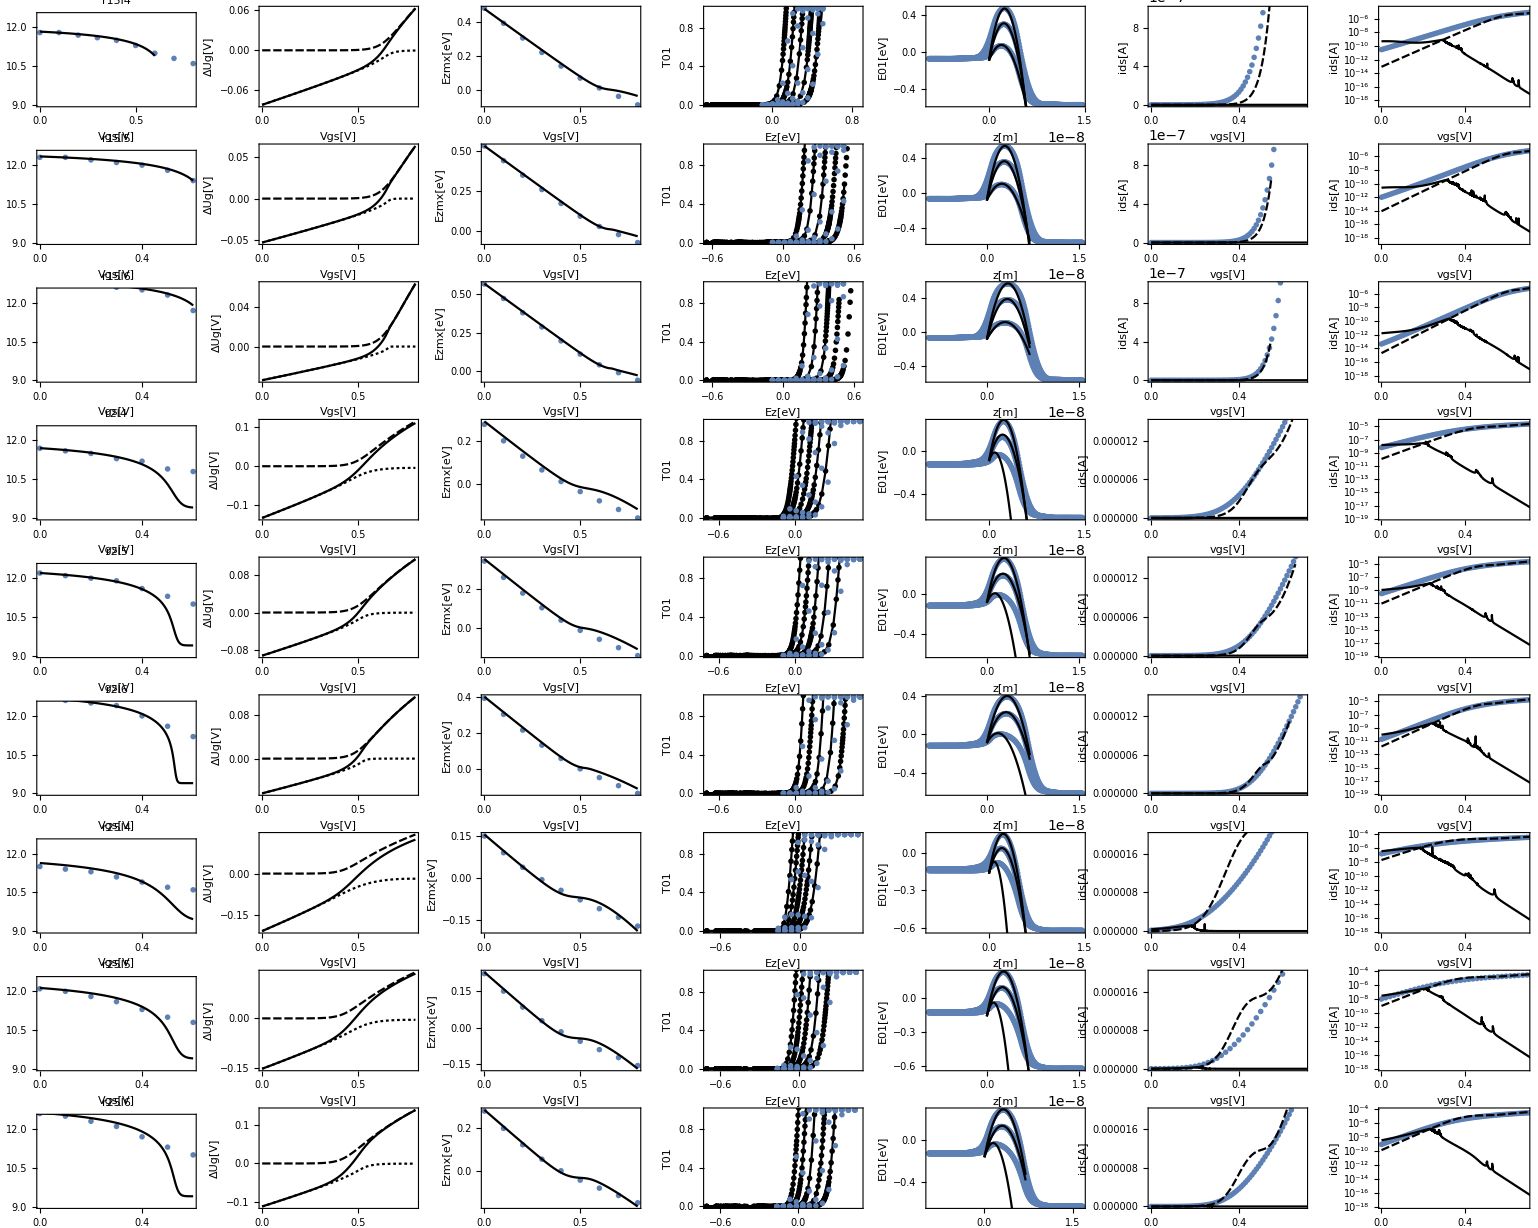
```mathematica
Block[{(*fitting energy level*)a1=0.95,(*fitting transmission coefficient*)a2=1.5,(*allzmax2, fitting barrier top*)b=.5,aa=(8 Pi^4 hbar^2 esi^2)/(subbandtable[[1,1]]^2 e^3 mt)},
(********************************************************************************(((((( Model expressions )))))))*)
(* parameters *)A[r_,l_]:=(VBI[[r]]-vgs+wgc-wfb) (1-Exp[-gm2[[r]] L[[l]]])+VDS5;B[r_,l_]:=(VBI[[r]]-vgs+wgc-wfb) (Exp[gm2[[r]] L[[l]]]-1)-VDS5;bb[r_]:=subbandtable[[1,5]]+(4 Pi esi)/cox[[r]]-.5;cc[r_]:=-wgc+wfb-subbandtable[[1,3,r]];
(* expression of the barrier top locations in all operating regions *)allzmax2[r_,l_]:=Re[1/(2 gm2[[r]]) Log[1+1/b Log[1+Exp[b B[r,l]/A[r,l]]]]];
(*zmax[r_,l_]:=Re[1/(2 gm2[[r]]) Log[B[r,l]/A[r,l]]];*)
(* expression of the dibl delta Ug for the subthreshold region at source *)augz2[r_,l_]:=Re[NN[[r]]((A[r,l]+B[r,l]) (-1/((4 Pi esi)/cox[[r]]+.5)))/(Exp[gm2[[r]] L[[l]]]-Exp[-gm2[[r]] L[[l]]])];
(* expression of delta Ug in the inversion region *)U[r_]:=Re[bb[r]/(2 aa) (-1+Sqrt[1+(4 aa)/(bb[r] bb[r]) 1/25 Log[1+Exp[25 (vgs+cc[r])]]])];
(* expression of delta Ug in all operating region *)conaugzmx2[r_,l_]:=Re[2 NN[[r]]/(Exp[gm2[[r]] L[[l]]]-Exp[-gm2[[r]] L[[l]]]) Sqrt[1/a1 Log[1+Exp[a1 A[r,l] B[r,l]]]] (-1/((4 Pi esi)/cox[[r]]+0.5))]+U[r];
(* expression of the lowest subband energy level at the source *)Eq201[r_,l_]:=-e (vgs-wgc+wfb)+kB T subbandtable[[1,4,r]]+e ((4 Pi esi)/cox[[r]]-.5+subbandtable[[1,5]]) augz2[r,l];
(* expression of the lowest subband energy level at the barrier top location *)Eq01zmx2[r_,l_]:=-e (vgs-wgc+wfb)+kB T subbandtable[[1,4,r]]+e ((4 Pi esi)/cox[[r]]-.5+subbandtable[[1,5]]) conaugzmx2[r,l];
(* expression of the lowest subband energy level using parabolic approximation *)Parab2Eq01[r_,l_]:=-((Eq01zmx2[r,l]-Eq201[r,l])/allzmax2[r,l]^2) (z-allzmax2[r,l])^2+Eq01zmx2[r,l];
(* expression of the transmission coefficient for source-to-drain tunneling in all operating regions *)allunitranscoe2[r_,l_]:=Re[(Exp[-1/a2 Log[1+Exp[(a2 Pi)/hbar Sqrt[(2 mt)/(Eq01zmx2[r,l]-Eq201[r,l])] allzmax2[r,l] ((Eq01zmx2[r,l]-Eq201[r,l])-Ez)]]])];
(* expression of the ballistic drain current *)ids[r_,l_]:=Re[e/(Pi hbar) subbandtable[[1,1]] NIntegrate[allunitranscoe2[r,l]/(1+Exp[(Eq201[r,l]+Ez)/(kB T)]),{Ez,0,2 e}]];
(******************************************************************************** Export Model Data*)
(*(*################################################################################## ((((( r15l3)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r1p5nml3nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[1,4]/nm},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml3nm/mathematica/zmxSLVC.txt",{r15l3zmxvgs[[#,4]],r15l3zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r1p5nml3nm/mathematica/conaugzmx2.txt",Table[{vgs,allzmax2[1,4]/nm},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r1p5nml3nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[1,4]/e},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml3nm/mathematica/zmxenglvlSLVC.txt",{r15l3zmxenglvl[[#,1]],r15l3zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r15l3transcoe0[[#,1]],r15l3transcoe0[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r15l3transcoe1[[#,1]],r15l3transcoe1[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r15l3transcoe2[[#,1]],r15l3transcoe2[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r15l3transcoe3[[#,1]],r15l3transcoe3[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r15l3transcoe4[[#,1]],r15l3transcoe4[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r1p5nml3nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r15l3transcoe5[[#,1]],r15l3transcoe5[[#,2]]}&/@Range[1,150,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r1p5nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[1,4]/e}/.vgs->0,{z,0,L,.01 L}],"CSV"];Export["./r1p5nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[1,4]/e}/.vgs->0.2,{z,0,L,.01 L}],"CSV"];
Export["./r1p5nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[1,4]/e}/.vgs->0.5,{z,0,L,.01 L}],"CSV"];Export["./r1p5nml3nm/mathematica/englvlz00SLVC",{r15l3englvlz00[[#,1]],r15l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
Export["./r1p5nml3nm/mathematica/englvlz02SLVC",{r15l3englvlz02[[#,1]],r15l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];Export["./r1p5nml3nm/mathematica/englvlz05SLVC",{r15l3englvlz05[[#,1]],r15l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
(*export the expression of total current*)Export["./r1p5nml3nm/mathematica/current.txt",Table[{vgs,ids[1,4]},{vgs,0,1,0.05}],"CSV"];Export["./r1p5nml3nm/mathematica/current-ua.txt",Table[{vgs,ids[1,4] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r1p5nml3nm/mathematica/currentSLVC.txt",{r15l3idsvgs[[#,1]],r15l3idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r1p5nml3nm/mathematica/currentSLVC-ua.txt",{r15l3idsvgs[[#,1]] ,r15l3idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];*)
(*################################################################################## ((((( r15l4)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r1p5nml4nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[1,1]/nm},{vgs,0,1,.01}],"CSV"];
Export["./r1p5nml4nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[1]])  Log[B[1,1]/A[1,1]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml4nm/mathematica/zmxSLVC.txt",{r15l4zmxvgs[[#,1]],r15l4zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r1p5nml4nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[1,1]},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml4nm/mathematica/augzmx2.txt",Table[{vgs,U[1]},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml4nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[1,1]-U[1]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r1p5nml4nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[1,1]/e},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml4nm/mathematica/zmxenglvlSLVC.txt",{r15l4zmxenglvl[[#,1]],r15l4zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r15l4transcoe0[[#,1]],r15l4transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r15l4transcoe1[[#,1]],r15l4transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r15l4transcoe2[[#,1]],r15l4transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r15l4transcoe3[[#,1]],r15l4transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r15l4transcoe4[[#,1]],r15l4transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml4nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r15l4transcoe5[[#,1]],r15l4transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r1p5nml4nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[1,1]/e}/.vgs->0,{z,0,L[[1]],.01 L[[1]]}],"CSV"];Export["./r1p5nml4nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[1,1]/e}/.vgs->0.2,{z,0,L[[1]],.01 L[[1]]}],"CSV"];
Export["./r1p5nml4nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[1,1]/e}/.vgs->0.5,{z,0,L[[1]],.01 L[[1]]}],"CSV"];Export["./r1p5nml4nm/mathematica/englvlz00SLVC.txt",{r15l4englvlz00[[#,1]],r15l4englvlz00[[#,2]]}&/@Range[1,241,1],"CSV"];
Export["./r1p5nml4nm/mathematica/englvlz02SLVC.txt",{r15l4englvlz02[[#,1]],r15l4englvlz02[[#,2]]}&/@Range[1,241,1],"CSV"];Export["./r1p5nml4nm/mathematica/englvlz05SLVC.txt",{r15l4englvlz05[[#,1]],r15l4englvlz05[[#,2]]}&/@Range[1,241,1],"CSV"];
(*export the expression of total current*)Export["./r1p5nml4nm/mathematica/current.txt",Table[{vgs,ids[1,1]},{vgs,0,1,0.05}],"CSV"];Export["./r1p5nml4nm/mathematica/current-ua.txt",Table[{vgs,ids[1,1] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r1p5nml4nm/mathematica/currentSLVC.txt",{r15l4idsvgs[[#,1]],r15l4idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r1p5nml4nm/mathematica/currentSLVC-ua.txt",{r15l4idsvgs[[#,1]] ,r15l4idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*################################################################################## ((((( r15l5)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r1p5nml5nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[1,2]/nm},{vgs,0,1,.01}],"CSV"];
Export["./r1p5nml5nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[1]])  Log[B[1,2]/A[1,2]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml5nm/mathematica/zmxSLVC.txt",{r15l5zmxvgs[[#,1]],r15l5zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r1p5nml5nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[1,2]},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml5nm/mathematica/augzmx2.txt",Table[{vgs,U[1]},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml5nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[1,2]-U[1]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r1p5nml5nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[1,2]/e},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml5nm/mathematica/zmxenglvlSLVC.txt",{r15l5zmxenglvl[[#,1]],r15l5zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r15l5transcoe0[[#,1]],r15l5transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r15l5transcoe1[[#,1]],r15l5transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r15l5transcoe2[[#,1]],r15l5transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r15l5transcoe3[[#,1]],r15l5transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r15l5transcoe4[[#,1]],r15l5transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml5nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r15l5transcoe5[[#,1]],r15l5transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r1p5nml5nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[1,2]/e}/.vgs->0,{z,0,L[[2]],.01 L[[2]]}],"CSV"];Export["./r1p5nml5nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[1,2]/e}/.vgs->0.2,{z,0,L[[2]],.01 L[[2]]}],"CSV"];
Export["./r1p5nml5nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[1,2]/e}/.vgs->0.5,{z,0,L[[2]],.01 L[[2]]}],"CSV"];Export["./r1p5nml5nm/mathematica/englvlz00SLVC.txt",{r15l5englvlz00[[#,1]],r15l5englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
Export["./r1p5nml5nm/mathematica/englvlz02SLVC.txt",{r15l5englvlz02[[#,1]],r15l5englvlz02[[#,2]]}&/@Range[1,251,1],"CSV"];vgsExport["./r1p5nml5nm/mathematica/englvlz05SLVC.txt",{r15l5englvlz05[[#,1]],r15l5englvlz05[[#,2]]}&/@Range[1,251,1],"CSV"];
(*export the expression of total current*)Export["./r1p5nml5nm/mathematica/current.txt",Table[{vgs,ids[1,2]},{vgs,0,1,0.05}],"CSV"];Export["./r1p5nml5nm/mathematica/current-ua.txt",Table[{vgs,ids[1,2] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r1p5nml5nm/mathematica/currentSLVC.txt",{r15l5idsvgs[[#,1]],r15l5idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r1p5nml5nm/mathematica/currentSLVC-ua.txt",{r15l5idsvgs[[#,1]] ,r15l5idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*################################################################################## ((((( r15l6)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r1p5nml6nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[1,3]/nm},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml6nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[1]])  Log[B[1,3]/A[1,3]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml6nm/mathematica/zmxSLVC.txt",{r15l6zmxvgs[[#,1]],r15l6zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r1p5nml6nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[1,3]},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml6nm/mathematica/augzmx2.txt",Table[{vgs,U[1]},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml6nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[1,3]-U[1]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r1p5nml6nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[1,3]/e},{vgs,0,1,.01}],"CSV"];Export["./r1p5nml6nm/mathematica/zmxenglvlSLVC.txt",{r15l6zmxenglvl[[#,1]],r15l6zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r15l6transcoe0[[#,1]],r15l6transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r15l6transcoe1[[#,1]],r15l6transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r15l6transcoe2[[#,1]],r15l6transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r15l6transcoe3[[#,1]],r15l6transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r15l6transcoe4[[#,1]],r15l6transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r1p5nml6nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r15l6transcoe5[[#,1]],r15l6transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r1p5nml6nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[1,3]/e}/.vgs->0,{z,0,L[[3]],.01 L[[3]]}],"CSV"];Export["./r1p5nml6nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[1,3]/e}/.vgs->0.2,{z,0,L[[3]],.01 L[[3]]}],"CSV"];
Export["./r1p5nml6nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[1,3]/e}/.vgs->0.5,{z,0,L[[3]],.01 L[[3]]}],"CSV"];Export["./r1p5nml6nm/mathematica/englvlz00SLVC.txt",{r15l6englvlz00[[#,1]],r15l6englvlz00[[#,2]]}&/@Range[1,261,1],"CSV"];
Export["./r1p5nml6nm/mathematica/englvlz02SLVC.txt",{r15l6englvlz02[[#,1]],r15l6englvlz02[[#,2]]}&/@Range[1,261,1],"CSV"];Export["./r1p5nml6nm/mathematica/englvlz05SLVC.txt",{r15l6englvlz05[[#,1]],r15l6englvlz05[[#,2]]}&/@Range[1,261,1],"CSV"];
(*export the expression of total current*)Export["./r1p5nml6nm/mathematica/current.txt",Table[{vgs,ids[1,3]},{vgs,0,1,0.05}],"CSV"];Export["./r1p5nml6nm/mathematica/current-ua.txt",Table[{vgs,ids[1,3] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r1p5nml6nm/mathematica/currentSLVC.txt",{r15l6idsvgs[[#,1]],r15l6idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r1p5nml6nm/mathematica/currentSLVC-ua.txt",{r15l6idsvgs[[#,1]] ,r15l6idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*(*################################################################################## ((((( r2l3)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2nml3nm/mathematica/allzmx.txt",Table[{vgs,allvgszmax2[2,4]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2nml3nm/mathematica/zmxSLVC.txt",{r2l3zmxvgs[[#,1]],r2l3zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2nml3nm/mathematica/conaugzmx2.txt",Table[{vgs,allzmax2[2,4]/nm},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2nml3nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[2,4]/e},{vgs,0,1,.01}],"CSV"];Export["./r2nml3nm/mathematica/zmxenglvlSLVC.txt",{r2l3zmxenglvl[[#,1]],r2l3zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r2nml3nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml3nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml3nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml3nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml3nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml3nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml3nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r2l3transcoe0[[#,1]],r2l3transcoe0[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2nml3nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r2l3transcoe1[[#,1]],r2l3transcoe1[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r2nml3nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r2l3transcoe2[[#,1]],r2l3transcoe2[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2nml3nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r2l3transcoe3[[#,1]],r2l3transcoe3[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r2nml3nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r2l3transcoe4[[#,1]],r2l3transcoe4[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2nml3nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r2l3transcoe5[[#,1]],r2l3transcoe5[[#,2]]}&/@Range[1,150,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[2,4]/e}/.vgs->0,{z,0,L,.01 L}],"CSV"];Export["./r2nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[2,4]/e}/.vgs->0.2,{z,0,L,.01 L}],"CSV"];
Export["./r2nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[2,4]/e}/.vgs->0.5,{z,0,L,.01 L}],"CSV"];Export["./r2nml3nm/mathematica/englvlz00SLVC",{r2l3englvlz00[[#,1]],r2l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
Export["./r2nml3nm/mathematica/englvlz02SLVC",{r2l3englvlz02[[#,1]],r2l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];Export["./r2nml3nm/mathematica/englvlz05SLVC",{r2l4englvlz05[[#,1]],r2l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
(*export the expression of total current*)Export["./r2nml3nm/mathematica/current.txt",Table[{vgs,ids[2,4]},{vgs,0,1,0.05}],"CSV"];Export["./r2nml3nm/mathematica/current-ua.txt",Table[{vgs,ids[2,4] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2nml3nm/mathematica/currentSLVC.txt",{r2l3idsvgs[[#,1]],r2l3idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2nml3nm/mathematica/currentSLVC-ua.txt",{r2l3idsvgs[[#,1]] ,r2l3idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];*)
(*################################################################################## ((((( r2l4)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2nml4nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[2,1]/nm},{vgs,0,1,.01}],"CSV"];
Export["./r2nml4nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[2]])  Log[B[2,1]/A[2,1]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2nml4nm/mathematica/zmxSLVC.txt",{r2l4zmxvgs[[#,1]],r2l4zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2nml4nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[2,1]},{vgs,0,1,.01}],"CSV"];Export["./r2nml4nm/mathematica/augzmx2.txt",Table[{vgs,U[2]},{vgs,0,1,.01}],"CSV"];Export["./r2nml4nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[2,1]-U[2]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2nml4nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[2,1]/e},{vgs,0,1,.01}],"CSV"];Export["./r2nml4nm/mathematica/zmxenglvlSLVC.txt",{r2l4zmxenglvl[[#,1]],r2l4zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r2nml4nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml4nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml4nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml4nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml4nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml4nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml4nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r2l4transcoe0[[#,1]],r2l4transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml4nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r2l4transcoe1[[#,1]],r2l4transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2nml4nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r2l4transcoe2[[#,1]],r2l4transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml4nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r2l4transcoe3[[#,1]],r2l4transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2nml4nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r2l4transcoe4[[#,1]],r2l4transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml4nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r2l4transcoe5[[#,1]],r2l4transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2nml4nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[2,1]/e}/.vgs->0,{z,0,L[[1]],.01 L[[1]]}],"CSV"];Export["./r2nml4nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[2,1]/e}/.vgs->0.2,{z,0,L[[1]],.01 L[[1]]}],"CSV"];
Export["./r2nml4nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[2,1]/e}/.vgs->0.5,{z,0,L[[1]],.01 L[[1]]}],"CSV"];Export["./r2nml4nm/mathematica/englvlz00SLVC.txt",{r2l4englvlz00[[#,1]],r2l4englvlz00[[#,2]]}&/@Range[1,241,1],"CSV"];
Export["./r2nml4nm/mathematica/englvlz02SLVC.txt",{r2l4englvlz02[[#,1]],r2l4englvlz02[[#,2]]}&/@Range[1,241,1],"CSV"];Export["./r2nml4nm/mathematica/englvlz05SLVC.txt",{r2l4englvlz05[[#,1]],r2l4englvlz05[[#,2]]}&/@Range[1,241,1],"CSV"];
(*export the expression of total current*)Export["./r2nml4nm/mathematica/current.txt",Table[{vgs,ids[2,1]},{vgs,0,1,0.05}],"CSV"];Export["./r2nml4nm/mathematica/current-ua.txt",Table[{vgs,ids[2,1] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2nml4nm/mathematica/currentSLVC.txt",{r2l4idsvgs[[#,1]],r2l4idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2nml4nm/mathematica/currentSLVC-ua.txt",{r2l4idsvgs[[#,1]] ,r2l4idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*################################################################################## ((((( r2l5)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2nml5nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[2,2]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2nml5nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[2]])  Log[B[2,2]/A[2,2]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2nml5nm/mathematica/zmxSLVC.txt",{r2l5zmxvgs[[#,1]],r2l5zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2nml5nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[2,2]},{vgs,0,1,.01}],"CSV"];Export["./r2nml5nm/mathematica/augzmx2.txt",Table[{vgs,U[2]},{vgs,0,1,.01}],"CSV"];Export["./r2nml5nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[2,2]-U[2]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2nml5nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[2,2]/e},{vgs,0,1,.01}],"CSV"];Export["./r2nml5nm/mathematica/zmxenglvlSLVC.txt",{r2l5zmxenglvl[[#,1]],r2l5zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"]vgs
(*export the expression of transmission coefficient*)Export["./r2nml5nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml5nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml5nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml5nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml5nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml5nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml5nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r2l5transcoe0[[#,1]],r2l5transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml5nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r2l5transcoe1[[#,1]],r2l5transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2nml5nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r2l5transcoe2[[#,1]],r2l5transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml5nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r2l5transcoe3[[#,1]],r2l5transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2nml5nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r2l5transcoe4[[#,1]],r2l5transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml5nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r2l5transcoe5[[#,1]],r2l5transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];vgs
(*export the expression of parabolic energy level along z-direction*)Export["./r2nml5nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[2,2]/e}/.vgs->0,{z,0,L[[2]],.01 L[[2]]}],"CSV"];Export["./r2nml5nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[2,2]/e}/.vgs->0.2,{z,0,L[[2]],.01 L[[2]]}],"CSV"];
Export["./r2nml5nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[2,2]/e}/.vgs->0.5,{z,0,L[[2]],.01 L[[2]]}],"CSV"];Export["./r2nml5nm/mathematica/englvlz00SLVC.txt",{r2l5englvlz00[[#,1]],r2l5englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
Export["./r2nml5nm/mathematica/englvlz02SLVC.txt",{r2l5englvlz02[[#,1]],r2l5englvlz02[[#,2]]}&/@Range[1,251,1],"CSV"];Export["./r2nml5nm/mathematica/englvlz05SLVC.txt",{r2l5englvlz05[[#,1]],r2l5englvlz05[[#,2]]}&/@Range[1,251,1],"CSV"];
(*export the expression of total current*)Export["./r2nml5nm/mathematica/current.txt",Table[{vgs,ids[2,2]},{vgs,0,1,0.05}],"CSV"];Export["./r2nml5nm/mathematica/current-ua.txt",Table[{vgs,ids[2,2] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2nml5nm/mathematica/currentSLVC.txt",{r2l5idsvgs[[#,1]],r2l5idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2nml5nm/mathematica/currentSLVC-ua.txt",{r2l5idsvgs[[#,1]] ,r2l5idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*################################################################################## ((((( r2l6)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2nml6nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[2,3]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2nml6nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[2]])  Log[B[2,3]/A[2,3]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2nml6nm/mathematica/zmxSLVC.txt",{r2l6zmxvgs[[#,1]],r2l6zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2nml6nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[2,3]},{vgs,0,1,.01}],"CSV"];Export["./r2nml6nm/mathematica/augzmx2.txt",Table[{vgs,U[2]},{vgs,0,1,.01}],"CSV"];Export["./r2nml6nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[2,3]-U[2]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2nml6nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[2,3]/e},{vgs,0,1,.01}],"CSV"];Export["./r2nml6nm/mathematica/zmxenglvlSLVC.txt",{r2l6zmxenglvl[[#,1]],r2l6zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r2nml6nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml6nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml6nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml6nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml6nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2nml6nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2nml6nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r2l6transcoe0[[#,1]],r2l6transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml6nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r2l6transcoe1[[#,1]],r2l6transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2nml6nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r2l6transcoe2[[#,1]],r2l6transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml6nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r2l6transcoe3[[#,1]],r2l6transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2nml6nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r2l6transcoe4[[#,1]],r2l6transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2nml6nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r2l6transcoe5[[#,1]],r2l6transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2nml6nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[2,3]/e}/.vgs->0,{z,0,L[[3]],.01 L[[3]]}],"CSV"];Export["./r2nml6nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[2,3]/e}/.vgs->0.2,{z,0,L[[3]],.01 L[[3]]}],"CSV"];
Export["./r2nml6nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[2,3]/e}/.vgs->0.5,{z,0,L[[3]],.01 L[[3]]}],"CSV"];Export["./r2nml6nm/mathematica/englvlz00SLVC.txt",{r2l6englvlz00[[#,1]],r2l6englvlz00[[#,2]]}&/@Range[1,261,1],"CSV"];
Export["./r2nml6nm/mathematica/englvlz02SLVC.txt",{r2l6englvlz02[[#,1]],r2l6englvlz02[[#,2]]}&/@Range[1,261,1],"CSV"];Export["./r2nml6nm/mathematica/englvlz05SLVC.txt",{r2l6englvlz05[[#,1]],r2l6englvlz05[[#,2]]}&/@Range[1,261,1],"CSV"];
(*export the expression of total current*)Export["./r2nml6nm/mathematica/current.txt",Table[{vgs,ids[2,3]},{vgs,0,1,0.05}],"CSV"];Export["./r2nml6nm/mathematica/current-ua.txt",Table[{vgs,ids[2,3] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2nml6nm/mathematica/currentSLVC.txt",{r2l6idsvgs[[#,1]],r2l6idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2nml6nm/mathematica/currentSLVC-ua.txt",{r2l6idsvgs[[#,1]] ,r2l6idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*(*################################################################################## ((((( r25l3)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)
Export["./r2p5nml3nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[3,4]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml3nm/mathematica/zmxSLVC.txt",{r25l3zmxvgs[[#,1]],r25l3zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2p5nml3nm/mathematica/conaugzmx2.txt",Table[{vgs,allzmax2[3,4]/nm},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2p5nml3nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[3,4]/e},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml3nm/mathematica/zmxenglvlSLVC.txt",{r25l3zmxenglvl[[#,1]],r25l3zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"]vgs
(*export the expression of transmission coefficient*)Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r25l3transcoe0[[#,1]],r25l3transcoe0[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r25l3transcoe1[[#,1]],r25l3transcoe1[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r25l3transcoe2[[#,1]],r25l3transcoe2[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r25l3transcoe3[[#,1]],r25l3transcoe3[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r25l3transcoe4[[#,1]],r25l3transcoe4[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml3nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r25l3transcoe5[[#,1]],r25l3transcoe5[[#,2]]}&/@Range[1,150,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2p5nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[3,4]/e}/.vgs->0,{z,0,L,.01 L}],"CSV"];Export["./r2p5nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[3,4]/e}/.vgs->0.2,{z,0,L,.01 L}],"CSV"];vgs
Export["./r2p5nml3nm/mathematica/parab2Eq01.txt",Table[{z/nm,Parab2Eq01[3,4]/e}/.vgs->0.5,{z,0,L,.01 L}],"CSV"];Export["./r2p5nml3nm/mathematica/englvlz00SLVC",{r25l3englvlz00[[#,1]],r25l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
Export["./r2p5nml3nm/mathematica/englvlz02SLVC",{r25l3englvlz02[[#,1]],r25l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];Export["./r2p5nml3nm/mathematica/englvlz05SLVC",{r25l3englvlz05[[#,1]],r25l3englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
(*export the expression of total current*)Export["./r2p5nml3nm/mathematica/current.txt",Table[{vgs,ids[3,4]},{vgs,0,1,0.05}],"CSV"];Export["./r2p5nml3nm/mathematica/current-ua.txt",Table[{vgs,ids[3,4] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2p5nml3nm/mathematica/currentSLVC.txt",{r25l3idsvgs[[#,1]],r25l3idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2p5nml3nm/mathematica/currentSLVC-ua.txt",{r25l3idsvgs[[#,1]] ,r25l3idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];*)
(*################################################################################## ((((( r25l4)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2p5nml4nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[3,1]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml4nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[3]])  Log[B[3,1]/A[3,1]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml4nm/mathematica/zmxSLVC.txt",{r25l4zmxvgs[[#,1]],r25l4zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2p5nml4nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[3,1]},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml4nm/mathematica/augzmx2.txt",Table[{vgs,U[3]},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml4nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[3,1]-U[3]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2p5nml4nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[3,1]/e},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml4nm/mathematica/zmxenglvlSLVC.txt",{r25l4zmxenglvl[[#,1]],r25l4zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r25l4transcoe0[[#,1]],r25l4transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r25l4transcoe1[[#,1]],r25l4transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r25l4transcoe2[[#,1]],r25l4transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r25l4transcoe3[[#,1]],r25l4transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r25l4transcoe4[[#,1]],r25l4transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2p5nml4nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r25l4transcoe5[[#,1]],r25l4transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2p5nml4nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[3,1]/e}/.vgs->0,{z,0,L[[1]],.01 L[[1]]}],"CSV"];Export["./r2p5nml4nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[3,1]/e}/.vgs->0.2,{z,0,L[[1]],.01 L[[1]]}],"CSV"];
Export["./r2p5nml4nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[3,1]/e}/.vgs->0.5,{z,0,L[[1]],.01 L[[1]]}],"CSV"];Export["./r2p5nml4nm/mathematica/englvlz00SLVC.txt",{r25l4englvlz00[[#,1]],r25l4englvlz00[[#,2]]}&/@Range[1,241,1],"CSV"];
Export["./r2p5nml4nm/mathematica/englvlz02SLVC.txt",{r25l4englvlz02[[#,1]],r25l4englvlz02[[#,2]]}&/@Range[1,241,1],"CSV"];Export["./r2p5nml4nm/mathematica/englvlz05SLVC.txt",{r25l4englvlz05[[#,1]],r25l4englvlz05[[#,2]]}&/@Range[1,241,1],"CSV"];
(*export the expression of total current*)Export["./r2p5nml4nm/mathematica/current.txt",Table[{vgs,ids[3,1]},{vgs,0,1,0.05}],"CSV"];Export["./r2p5nml4nm/mathematica/current-ua.txt",Table[{vgs,ids[3,1] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2p5nml4nm/mathematica/currentSLVC.txt",{r25l4idsvgs[[#,1]],r25l4idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2p5nml4nm/mathematica/currentSLVC-ua.txt",{r25l4idsvgs[[#,1]] ,r25l4idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*################################################################################## ((((( r25l5)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2p5nml5nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[3,2]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml5nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[3]])  Log[B[3,2]/A[3,2]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml5nm/mathematica/zmxSLVC.txt",{r25l5zmxvgs[[#,1]],r25l5zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2p5nml5nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[3,2]},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml5nm/mathematica/augzmx2.txt",Table[{vgs,U[3]},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml5nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[3,2]-U[3]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2p5nml5nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[3,2]/e},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml5nm/mathematica/zmxenglvlSLVC.txt",{r25l5zmxenglvl[[#,1]],r25l5zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];vgs
Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r25l5transcoe0[[#,1]],r25l5transcoe0[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r25l5transcoe1[[#,1]],r25l5transcoe1[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r25l5transcoe2[[#,1]],r25l5transcoe2[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r25l5transcoe3[[#,1]],r25l5transcoe3[[#,2]]}&/@Range[1,150,1],"CSV"];
Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r25l5transcoe4[[#,1]],r25l5transcoe4[[#,2]]}&/@Range[1,150,1],"CSV"];Export["./r2p5nml5nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r25l5transcoe5[[#,1]],r25l5transcoe5[[#,2]]}&/@Range[1,150,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2p5nml5nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[3,2]/e}/.vgs->0,{z,0,L[[2]],.01 L[[2]]}],"CSV"];Export["./r2p5nml5nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[3,2]/e}/.vgs->0.2,{z,0,L[[2]],.01 L[[2]]}],"CSV"];
Export["./r2p5nml5nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[3,2]/e}/.vgs->0.5,{z,0,L[[2]],.01 L[[2]]}],"CSV"];Export["./r2p5nml5nm/mathematica/englvlz00SLVC.txt",{r25l5englvlz00[[#,1]],r25l5englvlz00[[#,2]]}&/@Range[1,251,1],"CSV"];
Export["./r2p5nml5nm/mathematica/englvlz02SLVC.txt",{r25l5englvlz02[[#,1]],r25l5englvlz02[[#,2]]}&/@Range[1,251,1],"CSV"];Export["./r2p5nml5nm/mathematica/englvlz05SLVC.txt",{r25l5englvlz05[[#,1]],r25l5englvlz05[[#,2]]}&/@Range[1,251,1],"CSV"];
(*export the expression of total current*)Export["./r2p5nml5nm/mathematica/current.txt",Table[{vgs,ids[3,2]},{vgs,0,1,0.05}],"CSV"];Export["./r2p5nml5nm/mathematica/current-ua.txt",Table[{vgs,ids[3,2] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2p5nml5nm/mathematica/currentSLVC.txt",{r25l5idsvgs[[#,1]],r25l5idsvgs[[#,2]]}&/@Range[1,51,1],"CSV"];Export["./r2p5nml5nm/mathematica/currentSLVC-ua.txt",{r25l5idsvgs[[#,1]] ,r25l5idsvgs[[#,2]] 10^6}&/@Range[1,51,1],"CSV"];
(*################################################################################## ((((( r25l6)))))*)
(*export the expression for calculating "allzmax" from the model results and SILVACO data*)Export["./r2p5nml6nm/mathematica/allzmx.txt",Table[{vgs,allzmax2[3,3]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml6nm/mathematica/orizmx.txt",Table[{vgs,1/(2 gm2[[3]])  Log[B[3,3]/A[3,3]]/nm},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml6nm/mathematica/zmxSLVC.txt",{r25l6zmxvgs[[#,1]],r25l6zmxvgs[[#,2]]-9.3}&/@Range[1,10,1],"CSV"];
(*export the expression of the delta Ug*)Export["./r2p5nml6nm/mathematica/conaugzmx2.txt",Table[{vgs,conaugzmx2[3,3]},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml6nm/mathematica/augzmx2.txt",Table[{vgs,U[3]},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml6nm/mathematica/diblugzmx2.txt",Table[{vgs,conaugzmx2[3,3]-U[3]},{vgs,0,1,.01}],"CSV"];
(*export the expression of energy level at the barrier top*)Export["./r2p5nml6nm/mathematica/Eq01zmx2.txt",Table[{vgs,Eq01zmx2[3,3]/e},{vgs,0,1,.01}],"CSV"];Export["./r2p5nml6nm/mathematica/zmxenglvlSLVC.txt",{r25l6zmxenglvl[[#,1]],r25l6zmxenglvl[[#,2]]}&/@Range[1,10,1],"CSV"];
(*export the expression of transmission coefficient*)Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs00.txt",Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs01.txt",Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0.1,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs02.txt",Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0.2,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs03.txt",Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0.3,{Ez,0,.6 e,.05 e}],"CSV"];-Graphics-
Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs04.txt",Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0.4,{Ez,0,.6 e,.05 e}],"CSV"];Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs05.txt",Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0.5,{Ez,0,.6 e,.05 e}],"CSV"];
Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs00SLVC.txt",{r25l6transcoe0[[#,1]],r25l6transcoe0[[#,2]]}&/@Range[1,200,1],"CSV"];vgsExport["./r2p5nml6nm/mathematica/allunitranscoe2vgs01SLVC.txt",{r25l6transcoe1[[#,1]],r25l6transcoe1[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs02SLVC.txt",{r25l6transcoe2[[#,1]],r25l6transcoe2[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs03SLVC.txt",{r25l6transcoe3[[#,1]],r25l6transcoe3[[#,2]]}&/@Range[1,200,1],"CSV"];
Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs04SLVC.txt",{r25l6transcoe4[[#,1]],r25l6transcoe4[[#,2]]}&/@Range[1,200,1],"CSV"];Export["./r2p5nml6nm/mathematica/allunitranscoe2vgs05SLVC.txt",{r25l6transcoe5[[#,1]],r25l6transcoe5[[#,2]]}&/@Range[1,200,1],"CSV"];
(*export the expression of parabolic energy level along z-direction*)Export["./r2p5nml6nm/mathematica/parab2Eq0100.txt",Table[{z/nm,Parab2Eq01[3,3]/e}/.vgs->0,{z,0,L[[3]],.01 L[[3]]}],"CSV"];Export["./r2p5nml6nm/mathematica/parab2Eq0102.txt",Table[{z/nm,Parab2Eq01[3,3]/e}/.vgs->0.2,{z,0,L[[3]],.01 L[[3]]}],"CSV"];
Export["./r2p5nml6nm/mathematica/parab2Eq0105.txt",Table[{z/nm,Parab2Eq01[3,3]/e}/.vgs->0.5,{z,0,L[[3]],.01 L[[3]]}],"CSV"];Export["./r2p5nml6nm/mathematica/englvlz00SLVC.txt",{r25l6englvlz00[[#,1]],r25l6englvlz00[[#,2]]}&/@Range[1,261,1],"CSV"];
Export["./r2p5nml6nm/mathematica/englvlz02SLVC.txt",{r25l6englvlz02[[#,1]],r25l6englvlz02[[#,2]]}&/@Range[1,261,1],"CSV"];Export["./r2p5nml6nm/mathematica/englvlz05SLVC.txt",{r25l6englvlz05[[#,1]],r25l6englvlz05[[#,2]]}&/@Range[1,261,1],"CSV"];
(*export the expression of total current*)Export["./r2p5nml6nm/mathematica/current.txt",Table[{vgs,ids[3,3]},{vgs,0,1,0.05}],"CSV"];Export["./r2p5nml6nm/mathematica/current-ua.txt",Table[{vgs,ids[3,3] 10^6},{vgs,0,1,0.05}],"CSV"];
Export["./r2p5nml6nm/mathematica/currentSLVC.txt",{r25l6idsvgs[[#,1]],r25l6idsvgs[[#,2]]}&/@Range[1,100,1],"CSV"];Export["./r2p5nml6nm/mathematica/currentSLVC-ua.txt",{r25l6idsvgs[[#,1]] ,r25l6idsvgs[[#,2]] 10^6}&/@Range[1,100,1],"CSV"];
(*(((((((plot out figures)))))))*)
GraphicsGrid[{(*{Show[ListPlot[r15l3zmxvgs],Plot[allzmax2[1,4]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r15l3"],Plot[conaugzmx2[1,4],{vgs,0,.6},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r15l3zmxenglvl],Plot[Eq01zmx2[1,4]/e,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.6},All}],Show[ListLinePlot[{r15l3transcoe1[[#,1]],r15l3transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l3transcoe2[[#,1]],r15l3transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l3transcoe3[[#,1]],r15l3transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l3transcoe4[[#,1]],r15l3transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l3transcoe5[[#,1]],r15l3transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,4])/e,allunitranscoe2[1,4]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r15l3englvlz00[[#,1]]-9.4)/10^9,r15l3englvlz00[[#,2]]}&/@Range[1,231,1]],ListPlot[{(r15l3englvlz02[[#,1]]-9.4)/10^9,r15l3englvlz02[[#,2]]}&/@Range[1,231,1]],ListPlot[{(r15l3englvlz05[[#,1]]-9.4)/10^9,r15l3englvlz05[[#,2]]}&/@Range[1,231,1]],Plot[{Parab2Eq01[1,4]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r15l3idsvgs],Plot[{ids[1,4],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,4]/(kB T)]]},{vgs,0,.55}],Frame->True,FrameLabel->{"vgsvgs","ids[A]"},PlotRange->{{0,.55},{0,.00001}}],Show[ListLogPlot[r15l3idsvgs],LogPlot[{ids[1,4],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,4]/(kB T)]]},{vgs,0,.55}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.55},All}]},*){Show[ListPlot[r15l4zmxvgs],Plot[allzmax2[1,1]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.8},{9,12.5}},PlotLabel->"r15l4"],Plot[{conaugzmx2[1,1],U[1],conaugzmx2[1,1]-U[1]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r15l4zmxenglvl],Plot[Eq01zmx2[1,1]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r15l4transcoe1[[#,1]],r15l4transcoe1[[#,2]]}&/@Range[1,200,1]],ListLinePlot[{r15l4transcoe2[[#,1]],r15l4transcoe2[[#,2]]}&/@Range[1,200,1]],ListLinePlot[{r15l4transcoe3[[#,1]],r15l4transcoe3[[#,2]]}&/@Range[1,200,1]],ListLinePlot[{r15l4transcoe4[[#,1]],r15l4transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l4transcoe5[[#,1]],r15l4transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,1])/e,allunitranscoe2[1,1]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r15l4englvlz00[[#,1]]-9.4)/10^9,r15l4englvlz00[[#,2]]}&/@Range[1,241,1]],ListPlot[{(r15l4englvlz02[[#,1]]-9.4)/10^9,r15l4englvlz02[[#,2]]}&/@Range[1,241,1]],ListPlot[{(r15l4englvlz05[[#,1]]-9.4)/10^9,r15l4englvlz05[[#,2]]}&/@Range[1,241,1]],Plot[{Parab2Eq01[1,1]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r15l4idsvgs],Plot[{ids[1,1],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,1]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLavgsbel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.000001}}],Show[ListLogPlot[r15l4idsvgs],LogPlot[{ids[1,1],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,1]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},{Show[ListPlot[r15l5zmxvgs],Plot[allzmax2[1,2]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r15l5"],Plot[{conaugzmx2[1,2],U[1],conaugzmx2[1,2]-U[1]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r15l5zmxenglvl],Plot[Eq01zmx2[1,2]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r15l5transcoe1[[#,1]],r15l5transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l5transcoe2[[#,1]],r15l5transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l5transcoe3[[#,1]],r15l5transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l5transcoe4[[#,1]],r15l5transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l5transcoe5[[#,1]],r15l5transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,2])/e,allunitranscoe2[1,2]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r15l5englvlz00[[#,1]]-9.4)/10^9,r15l5englvlz00[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r15l5englvlz02[[#,1]]-9.4)/10^9,r15l5englvlz02[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r15l5englvlz05[[#,1]]-9.4)/10^9,r15l5englvlz05[[#,2]]}&/@Range[1,250,1]],Plot[{Parab2Eq01[1,2]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r15l5idsvgs],Plot[{ids[1,2],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,2]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.000001}}],Show[ListLogPlot[r15l5idsvgs],LogPlot[{ids[1,2],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,2]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},{Show[ListPlot[r15l6zmxvgs],Plot[allzmax2[1,3]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r15l6"],Plot[{conaugzmx2[1,3],U[1],conaugzmx2[1,3]-U[1]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r15l6zmxenglvl],Plot[Eq01zmx2[1,3]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r15l6transcoe1[[#,1]],r15l6transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l6transcoe2[[#,1]],r15l6transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l6transcoe3[[#,1]],r15l6transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l6transcoe4[[#,1]],r15l6transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r15l6transcoe5[[#,1]],r15l6transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[1,3])/e,allunitranscoe2[1,3]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r15l6englvlz00[[#,1]]-9.4)/10^9,r15l6englvlz00[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r15l6englvlz02[[#,1]]-9.4)/10^9,r15l6englvlz02[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r15l6englvlz05[[#,1]]-9.4)/10^9,r15l6englvlz05[[#,2]]}&/@Range[1,250,1]],Plot[{Parab2Eq01[1,3]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r15l6idsvgs],Plot[{ids[1,3],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,3]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.000001}}],Show[ListLogPlot[r15l6idsvgs],LogPlot[{ids[1,3],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[1,3]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},(*{Show[ListPlot[r2l3zmxvgs],Plot[allzmax2[2,4]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r2l3"],Plot[conaugzmx2[2,4],{vgs,0,.6},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r2l3zmxenglvl],Plot[Eq01zmx2[2,4]/e,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.6},All}],Show[ListLinePlot[{r2l3transcoe1[[#,1]],r2l3transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l3transcoe2[[#,1]],r2l3transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l3transcoe3[[#,1]],r2l3transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l3transcoe4[[#,1]],r2l3transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l3transcoe5[[#,1]],r2l3transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,4])/e,allunitranscoe2[2,4]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r2l3englvlz00[[#,1]]-9.4)/10^9,r2l3englvlz00[[#,2]]}&/@Range[1,231,1]],ListPlot[{(r2l3englvlz02[[#,1]]-9.4)/10^9,r2l3englvlz02[[#,2]]}&/@Range[1,231,1]],ListPlot[{(r2l3englvlz05[[#,1]]-9.4)/10^9,r2l3englvlz05[[#,2]]}&/@Range[1,231,1]],Plot[{Parab2Eq01[2,4]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r2l3idsvgs],Plot[{ids[2,4],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,4]/(kB T)]]},{vgs,0,.55}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.55},{0,.00001}}],Show[ListLogPlot[r2l3idsvgs],LogPlot[{ids[2,4],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,4]/(kB T)]]},{vgs,0,.55}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.55},All}]},*){Show[ListPlot[r2l4zmxvgs],Plot[allzmax2[2,1]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r2l4"],Plot[{conaugzmx2[2,1],U[2],conaugzmx2[2,1]-U[2]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r2l4zmxenglvl],Plot[Eq01zmx2[2,1]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r2l4transcoe1[[#,1]],r2l4transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l4transcoe2[[#,1]],r2l4transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l4transcoe3[[#,1]],r2l4transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l4transcoe4[[#,1]],r2l4transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l4transcoe5[[#,1]],r2l4transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,1])/e,allunitranscoe2[2,1]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r2l4englvlz00[[#,1]]-9.4)/10^9,r2l4englvlz00[[#,2]]}&/@Range[1,241,1]],ListPlot[{(r2l4englvlz02[[#,1]]-9.4)/10^9,r2l4englvlz02[[#,2]]}&/@Range[1,241,1]],ListPlot[{(r2l4englvlz05[[#,1]]-9.4)/10^9,r2l4englvlz05[[#,2]]}&/@Range[1,241,1]],Plot[{Parab2Eq01[2,1]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r2l4idsvgs],Plot[{ids[2,1],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,1]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.000015}}],Show[ListLogPlot[r2l4idsvgs],LogPlot[{ids[2,1],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,1]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},{Show[ListPlot[r2l5zmxvgs],Plot[allzmax2[2,2]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r2l5"],Plot[{conaugzmx2[2,2],U[2],conaugzmx2[2,2]-U[2]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r2l5zmxenglvl],Plot[Eq01zmx2[2,2]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r2l5transcoe1[[#,1]],r2l5transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l5transcoe2[[#,1]],r2l5transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l5transcoe3[[#,1]],r2l5transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l5transcoe4[[#,1]],r2l5transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l5transcoe5[[#,1]],r2l5transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,2])/e,allunitranscoe2[2,2]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r2l5englvlz00[[#,1]]-9.4)/10^9,r2l5englvlz00[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r2l5englvlz02[[#,1]]-9.4)/10^9,r2l5englvlz02[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r2l5englvlz05[[#,1]]-9.4)/10^9,r2l5englvlz05[[#,2]]}&/@Range[1,250,1]],Plot[{Parab2Eq01[2,2]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r2l5idsvgs],Plot[{ids[2,2],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,2]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.000015}}],Show[ListLogPlot[r2l5idsvgs],LogPlot[{ids[2,2],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,2]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},{Show[ListPlot[r2l6zmxvgs],Plot[allzmax2[2,3]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r2l6"],Plot[{conaugzmx2[2,3],U[2],conaugzmx2[2,3]-U[2]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r2l6zmxenglvl],Plot[Eq01zmx2[2,3]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r2l6transcoe1[[#,1]],r2l6transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l6transcoe2[[#,1]],r2l6transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l6transcoe3[[#,1]],r2l6transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l6transcoe4[[#,1]],r2l6transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r2l6transcoe5[[#,1]],r2l6transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[2,3])/e,allunitranscoe2[2,3]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r2l6englvlz00[[#,1]]-9.4)/10^9,r2l6englvlz00[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r2l6englvlz02[[#,1]]-9.4)/10^9,r2l6englvlz02[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r2l6englvlz05[[#,1]]-9.4)/10^9,r2l6englvlz05[[#,2]]}&/@Range[1,250,1]],Plot[{Parab2Eq01[2,3]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r2l6idsvgs],Plot[{ids[2,3],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,3]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.000015}}],Show[ListLogPlot[r2l6idsvgs],LogPlot[{ids[2,3],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[2,3]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},(*{Show[ListPlot[r25l3zmxvgs],Plot[allzmax2[3,4]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r25l3"],Plot[conaugzmx2[3,4],{vgs,0,.6},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r25l3zmxenglvl],Plot[Eq01zmx2[3,4]/e,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.6},All}],Show[ListLinePlot[{r25l3transcoe1[[#,1]],r25l3transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l3transcoe2[[#,1]],r25l3transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l3transcoe3[[#,1]],r25l3transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l3transcoe4[[#,1]],r25l3transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l3transcoe5[[#,1]],r25l3transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,4])/e,allunitranscoe2[3,4]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r25l3englvlz00[[#,1]]-9.4)/10^9,r25l3englvlz00[[#,2]]}&/@Range[1,231,1]],ListPlot[{(r25l3englvlz02[[#,1]]-9.4)/10^9,r25l3englvlz02[[#,2]]}&/@Range[1,231,1]],ListPlot[{(r25l3englvlz05[[#,1]]-9.4)/10^9,r25l3englvlz05[[#,2]]}&/@Range[1,231,1]],Plot[{Parab2Eq01[3,4]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r25l3idsvgs],Plot[{ids[3,4],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,4]/(kB T)]]},{vgs,0,.55}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.55},{0,.00001}}],Show[ListLogPlot[r25l3idsvgs],LogPlot[{ids[3,4],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,4]/(kB T)]]},{vgs,0,.55}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.55},All}]},*){Show[ListPlot[r25l4zmxvgs],Plot[allzmax2[3,1]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r25l4"],Plot[{conaugzmx2[3,1],U[3],conaugzmx2[3,1]-U[3]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r25l4zmxenglvl],Plot[Eq01zmx2[3,1]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r25l4transcoe1[[#,1]],r25l4transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l4transcoe2[[#,1]],r25l4transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l4transcoe3[[#,1]],r25l4transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l4transcoe4[[#,1]],r25l4transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l4transcoe5[[#,1]],r25l4transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,1])/e,allunitranscoe2[3,1]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r25l4englvlz00[[#,1]]-9.4)/10^9,r25l4englvlz00[[#,2]]}&/@Range[1,241,1]],ListPlot[{(r25l4englvlz02[[#,1]]-9.4)/10^9,r25l4englvlz02[[#,2]]}&/@Range[1,241,1]],ListPlot[{(r25l4englvlz05[[#,1]]-9.4)/10^9,r25l4englvlz05[[#,2]]}&/@Range[1,241,1]],Plot[{Parab2Eq01[3,1]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r25l4idsvgs],Plot[{ids[3,1],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,1]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.00002}}],Show[ListLogPlot[r25l4idsvgs],LogPlot[{ids[3,1],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,1]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},{Show[ListPlot[r25l5zmxvgs],Plot[allzmax2[3,2]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r25l5"],Plot[{conaugzmx2[3,2],U[3],conaugzmx2[3,2]-U[3]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r25l5zmxenglvl],Plot[Eq01zmx2[3,2]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r25l5transcoe1[[#,1]],r25l5transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l5transcoe2[[#,1]],r25l5transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l5transcoe3[[#,1]],r25l5transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l5transcoe4[[#,1]],r25l5transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l5transcoe5[[#,1]],r25l5transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,2])/e,allunitranscoe2[3,2]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r25l5englvlz00[[#,1]]-9.4)/10^9,r25l5englvlz00[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r25l5englvlz02[[#,1]]-9.4)/10^9,r25l5englvlz02[[#,2]]}&/@Range[1,250,1]],ListPlot[{(r25l5englvlz05[[#,1]]-9.4)/10^9,r25l5englvlz05[[#,2]]}&/@Range[1,250,1]],Plot[{Parab2Eq01[3,2]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r25l5idsvgs],Plot[{ids[3,2],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,2]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.00002}}],Show[ListLogPlot[r25l5idsvgs],LogPlot[{ids[3,2],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,2]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]},{Show[ListPlot[r25l6zmxvgs],Plot[allzmax2[3,3]/nm+9.4,{vgs,0,.6}],Frame->True,FrameLabel->{"Vgs[V]","zmx[nm]"},PlotRange->{{0,.6},{9,12.5}},PlotLabel->"r25l6"],Plot[{conaugzmx2[3,3],U[3],conaugzmx2[3,3]-U[3]},{vgs,0,.8},Frame->True,FrameLabel->{"Vgs[V]","ΔUg[V]"}],
Show[ListPlot[r25l6zmxenglvl],Plot[Eq01zmx2[3,3]/e,{vgs,0,.8}],Frame->True,FrameLabel->{"Vgs[V]","Ezmx[eV]"},PlotRange->{{0,.8},All}],Show[ListLinePlot[{r25l6transcoe1[[#,1]],r25l6transcoe1[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l6transcoe2[[#,1]],r25l6transcoe2[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l6transcoe3[[#,1]],r25l6transcoe3[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l6transcoe4[[#,1]],r25l6transcoe4[[#,2]]}&/@Range[1,150,1]],ListLinePlot[{r25l6transcoe5[[#,1]],r25l6transcoe5[[#,2]]}&/@Range[1,150,1]](*,ListLinePlot[{transcoe6[[#,1]] e,transcoe6[[#,2]]}&/@Range[1,150,1]]*),ListPlot[Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->0,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->.1,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->.2,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->.3,{Ez,0,.6 e,.05 e}]],ListPlot[Table[{(Ez+Eq201[3,3])/e,allunitranscoe2[3,3]}/.vgs->.4,{Ez,0,.6 e,.05 e}]],Frame->True,FrameLabel->{"Ez[eV]","T01"},PlotRange->{All,{0,1}}],Show[ListPlot[{(r25l6englvlz00[[#,1]]-9.4)/10^9,r25l6englvlz00[[#,2]]}&/@Range[1,261,1]],ListPlot[{(r25l6englvlz02[[#,1]]-9.4)/10^9,r25l6englvlz02[[#,2]]}&/@Range[1,261,1]],ListPlot[{(r25l6englvlz05[[#,1]]-9.4)/10^9,r25l6englvlz05[[#,2]]}&/@Range[1,261,1]],Plot[{Parab2Eq01[3,3]/e/.vgs->{0,.2,.5}},{z,0,7 nm}],Frame->True,FrameLabel->{"z[m]","E01[eV]"}],Show[ListPlot[r25l6idsvgs],Plot[{ids[3,3],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,3]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},{0,.00002}}],Show[ListLogPlot[r25l6idsvgs],LogPlot[{ids[3,3],(e kB T)/(Pi hbar) subbandtable[[1,1]] Log[1+Exp[-Eq01zmx2[3,3]/(kB T)]]},{vgs,0,.8}],Frame->True,FrameLabel->{"vgs[V]","ids[A]"},PlotRange->{{0,.7},All}]}}](*;
Plot[{(*allunitranscoe2[2,2]*)Eq01zmx2[2,2]-Eq201[2,2]}(*/.vgs->{0,.2,.5,.6}*),{vgs,0,1}]*)(*Print[{(-1/((4 Pi esi)/cox+.5)),(A+B) (-1/((4 Pi esi)/cox+.5))}]*)]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {4.20502×10^-21}. NIntegrate obtained 3.55867×10^-25+0. ⅈ and 1.77982×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {4.42335×10^-21}. NIntegrate obtained 4.55582×10^-26+0. ⅈ and 2.72316×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {1.78852×10^-20}. NIntegrate obtained 3.74579×10^-27+0. ⅈ and 5.05751×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-771.726] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-844.565] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics-